```mathematica
fileName = FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}];
(*RadioButtonBar[
Dynamic[fileName],
{
FileNameJoin[{NotebookDirectory[],"optimizerHistory.json"}],
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]*)
```

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

```mathematica
runningBest = FoldList[Max,First[#],Rest[#]]&[raw[[All,"maximizeMe"]]];
```

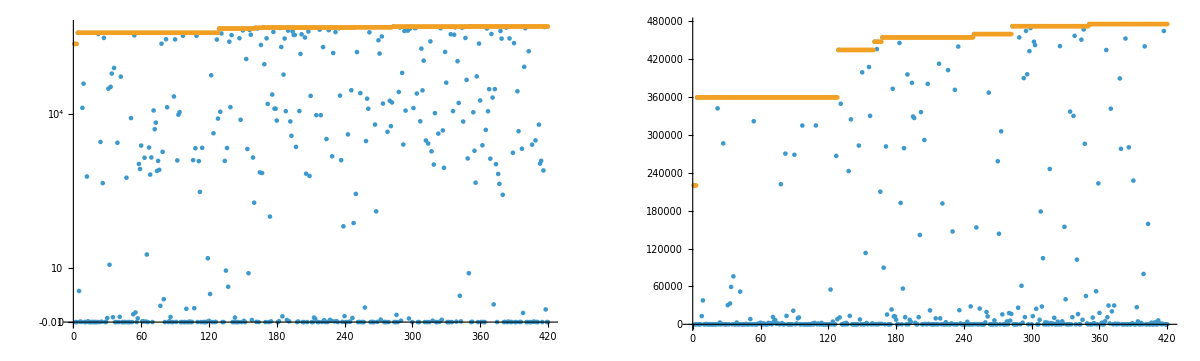

```mathematica
GraphicsGrid[{{
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
{
#["maximizeMe"]&/@raw,
runningBest
},
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -22.061802025
L2PhaseSet : -36.4693524278
L3PhaseSet : 0.1401168139
Q19851kG : -38.9554771303
Q19871kG : 31.8374520028
B1EkG : 4.5323507913
B2EkG : -6.5358876765
B3EkG : 2.0437637061
Q1EkG : 89.1501051182
Q2EkG : -96.0917428171
Q3EkG : 73.1319272705
Q4EkG : 61.6629885976
Q5EkG : -1.0503784742
Q6EkG : -97.4348525812
S1ELkG : 1065.5475633815
S2ELkG : -6796.2533521276
S3ELkG : -623.5030604544
S3ERkG : -465.7530623821
S2ERkG : -4391.9627941196
S1ERkG : 430.1961607341
S1EL_xOffset : 0.0001067316
S1EL_yOffset : -0.0002850138
S2EL_xOffset : 0.0002912934
S2EL_yOffset : -0.0001554853
S2ER_xOffset : -0.0004801294
S2ER_yOffset : 0.0002532963
S1ER_xOffset : 0.0003396801
S1ER_yOffset : 0.0003759627
PDrive_median_x : 0.0000445287
PDrive_median_y : 9.0329e-6
PDrive_median_xp : 0.0001852294
PDrive_median_yp : -1.961e-7
PDrive_median_energy : 6.040052251649707794e9
PDrive_sigmaSI90_x : 0.0000706237
PDrive_sigmaSI90_y : 0.0000310397
PDrive_sigmaSI90_z : 4.9939e-6
PDrive_sigmaSI90_xp : 0.0003779162
PDrive_sigmaSI90_yp : 0.0000329464
PDrive_sigmaSI90_energy : 6.8112110882991999e7
PDrive_emitSI90_x : 0.0003089053
PDrive_emitSI90_y : 0.0000119538
PDrive_norm_emit_x : 0.0000233858
PDrive_norm_emit_y : 6.8049e-6
PDrive_zCentroid : 991.3312661306
PDrive_charge_nC : 1.20472352
PDrive_BMAG_x : 1.8970991633
PDrive_BMAG_y : 1.1618013076
PDrive_sliced_BMAG_x : List(15.1358678901,4.865846103,3.1206837915,2.138301256,2.6711297505)
PDrive_sliced_BMAG_y : List(1.9792823235,1.8692915758,1.4759579661,1.0166010969,4.6845602742)
PWitness_median_x : 0.0000465311
PWitness_median_y : -1.8805e-6
PWitness_median_xp : -0.0004052929
PWitness_median_yp : 0.0000358215
PWitness_median_energy : 5.87880267793016243e9
PWitness_sigmaSI90_x : 0.0000688941
PWitness_sigmaSI90_y : 0.0000246168
PWitness_sigmaSI90_z : 4.7884e-6
PWitness_sigmaSI90_xp : 0.0001386742
PWitness_sigmaSI90_yp : 0.0000596126
PWitness_sigmaSI90_energy : 7.188250841953617e6
PWitness_emitSI90_x : 0.0000189832
PWitness_emitSI90_y : 0.0000105687
PWitness_norm_emit_x : 0.0000195534
PWitness_norm_emit_y : 6.0086e-6
PWitness_zCentroid : 991.3313009086
PWitness_charge_nC : 0.39608352
PWitness_BMAG_x : 5.3546497741
PWitness_BMAG_y : 1.4018173709
PWitness_sliced_BMAG_x : List(7.9989867009,8.7801856982,9.2866455527,6.8485374037,11.4691657037)
PWitness_sliced_BMAG_y : List(1.2186944874,1.4013013042,2.0118778973,2.0134336794,1.2192446833)
bunchSpacing : 0.0000347781
transverseCentroidOffset : 0.0000110955
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.
errorTerm_secondaryObjective : 0.000018919
maximizeMe : 475711.6165936516
inputBeamFilePathSuffix : "/beams/2025-05-13_twobunch_unoptimized_shortSpacing/2025-05-13_twobunch_unoptimized_shortSpacing.h5"
csrTF : False

```mathematica
(*Not tested to be robust... beware!*)
indepVarKeys = Keys[raw[[1]]][[1;;(Position[Keys[raw[[1]]],"PDrive_median_x"][[1,1]]-1)]]
```

{L1PhaseSet,L2PhaseSet,L3PhaseSet,Q19851kG,Q19871kG,B1EkG,B2EkG,B3EkG,Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S2ELkG,S3ELkG,S3ERkG,S2ERkG,S1ERkG,S1EL_xOffset,S1EL_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S1ER_xOffset,S1ER_yOffset}

## Plot specific

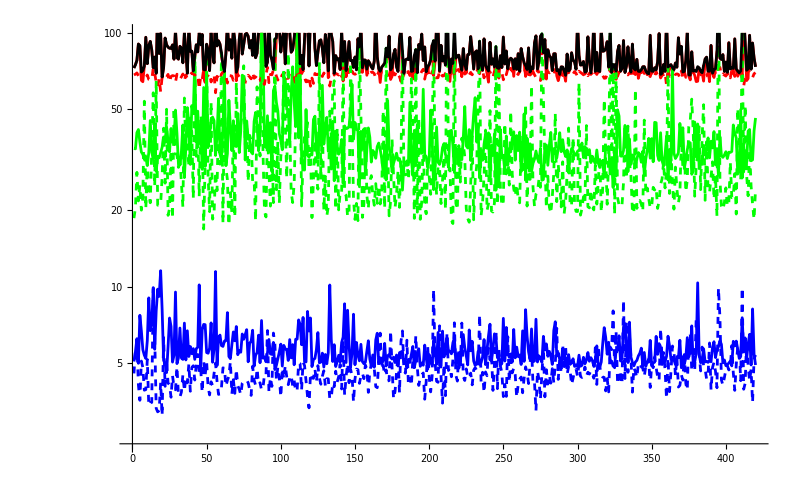

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

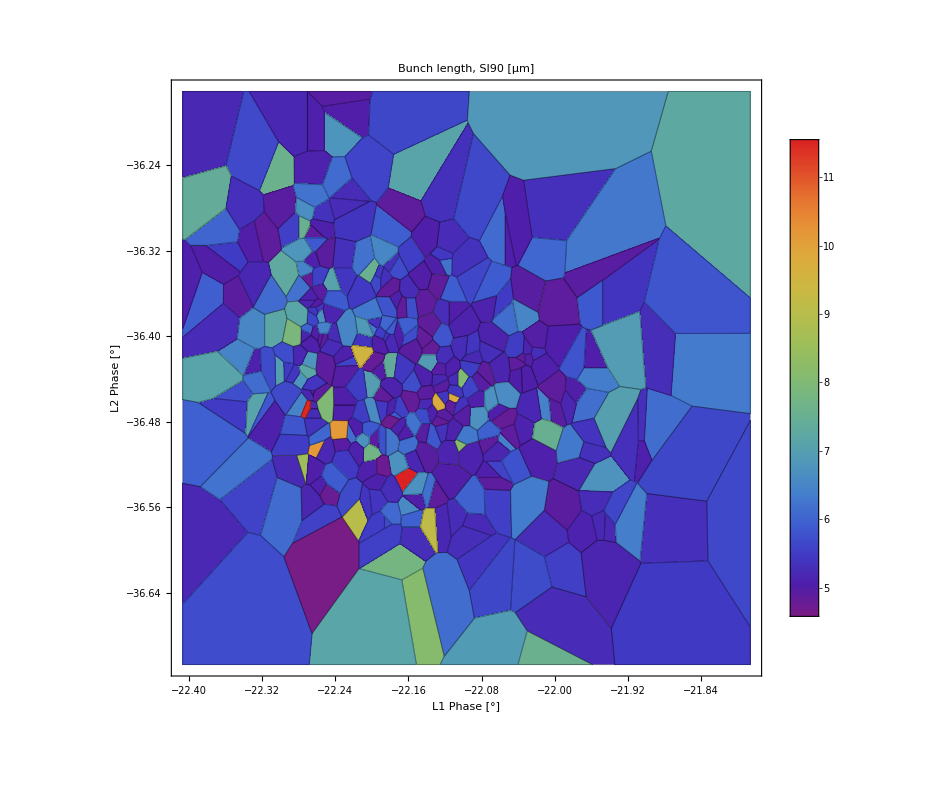

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,
PlotRange->{All,50},
(*PlotRange->{{-35,-21},{-50,-30},{All,50}},*)
Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"Bunch length, SI90 [μm]",LabelStyle->20]
```

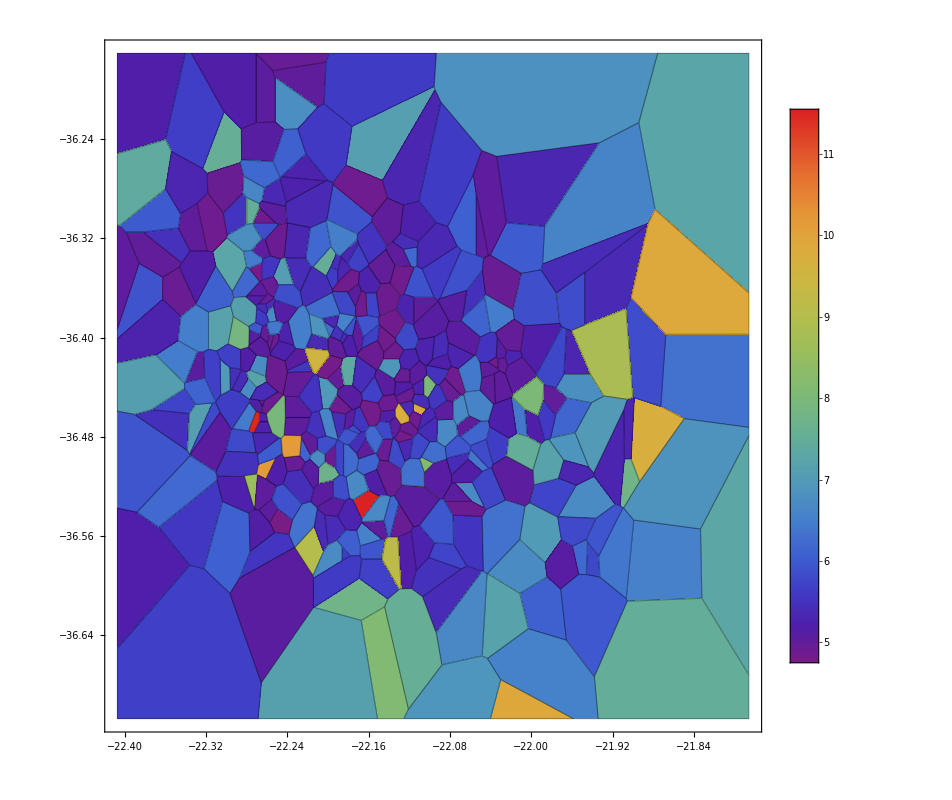

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

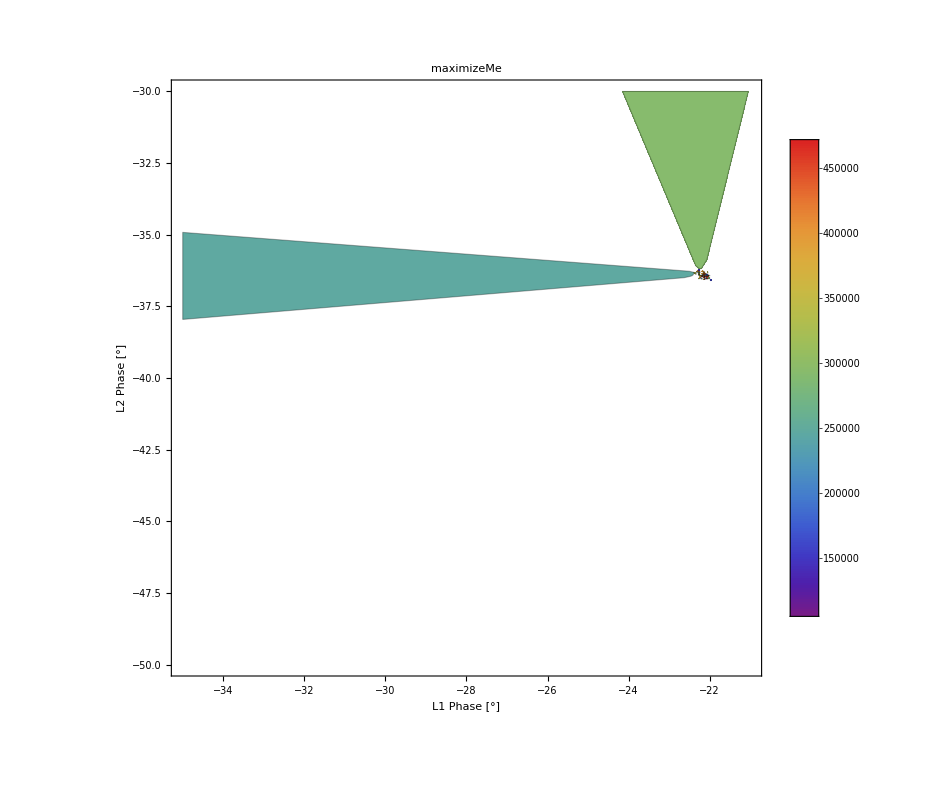

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
#["maximizeMe"]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",
InterpolationOrder->0,
(*PlotRange->{1*^5,All},*)
PlotRange->{{-35,-21},{-50,-30},{1*^5,All}},
Mesh->All,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},PlotLabel->"maximizeMe",LabelStyle->20]
```

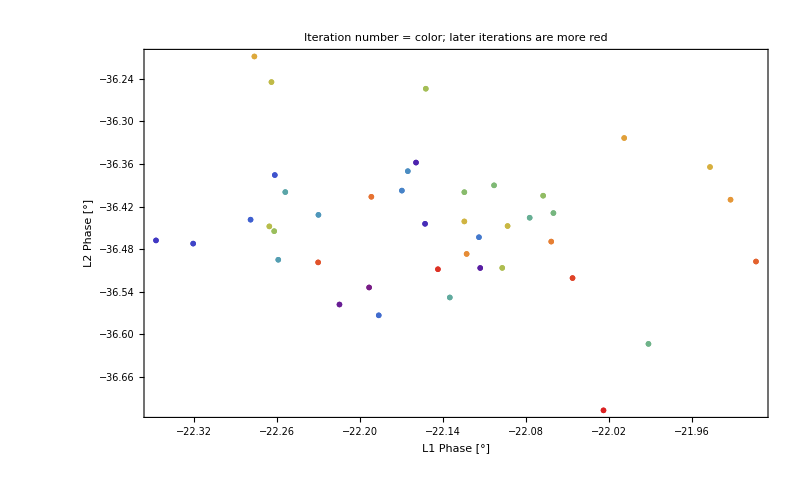

```mathematica
toPlot = {
#["L1PhaseSet"],
#["L2PhaseSet"]
}&/@raw[[1;;-1;;10]];
colors = Table[ColorData["Rainbow"][Rescale[i,{1,Length[toPlot]}]],{i,Length[toPlot]}];

ListPlot[{#}&/@toPlot,
ImageSize->800,
FrameLabel->{"L1 Phase [°]","L2 Phase [°]"},
LabelStyle->20,
Frame->True,
PlotStyle->colors,
PlotLabel->"Iteration number = color; later iterations are more red",
PlotMarkers->{Graphics[Disk[]],0.01}
]
```

```mathematica
(*Show[
ListContourPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"],
(10^6#["PDrive_sigmaSI90_z"])
}&/@raw,
PlotLegends->Automatic,
ImageSize->800,
SphericalRegion->True,
Contours->{4,4.9,5,5.1,6}
],
ListPointPlot3D[
{
#["S1ELkG"],
#["S2ELkG"],
#["S3ELkG"]
}&/@raw
]
]*)
```

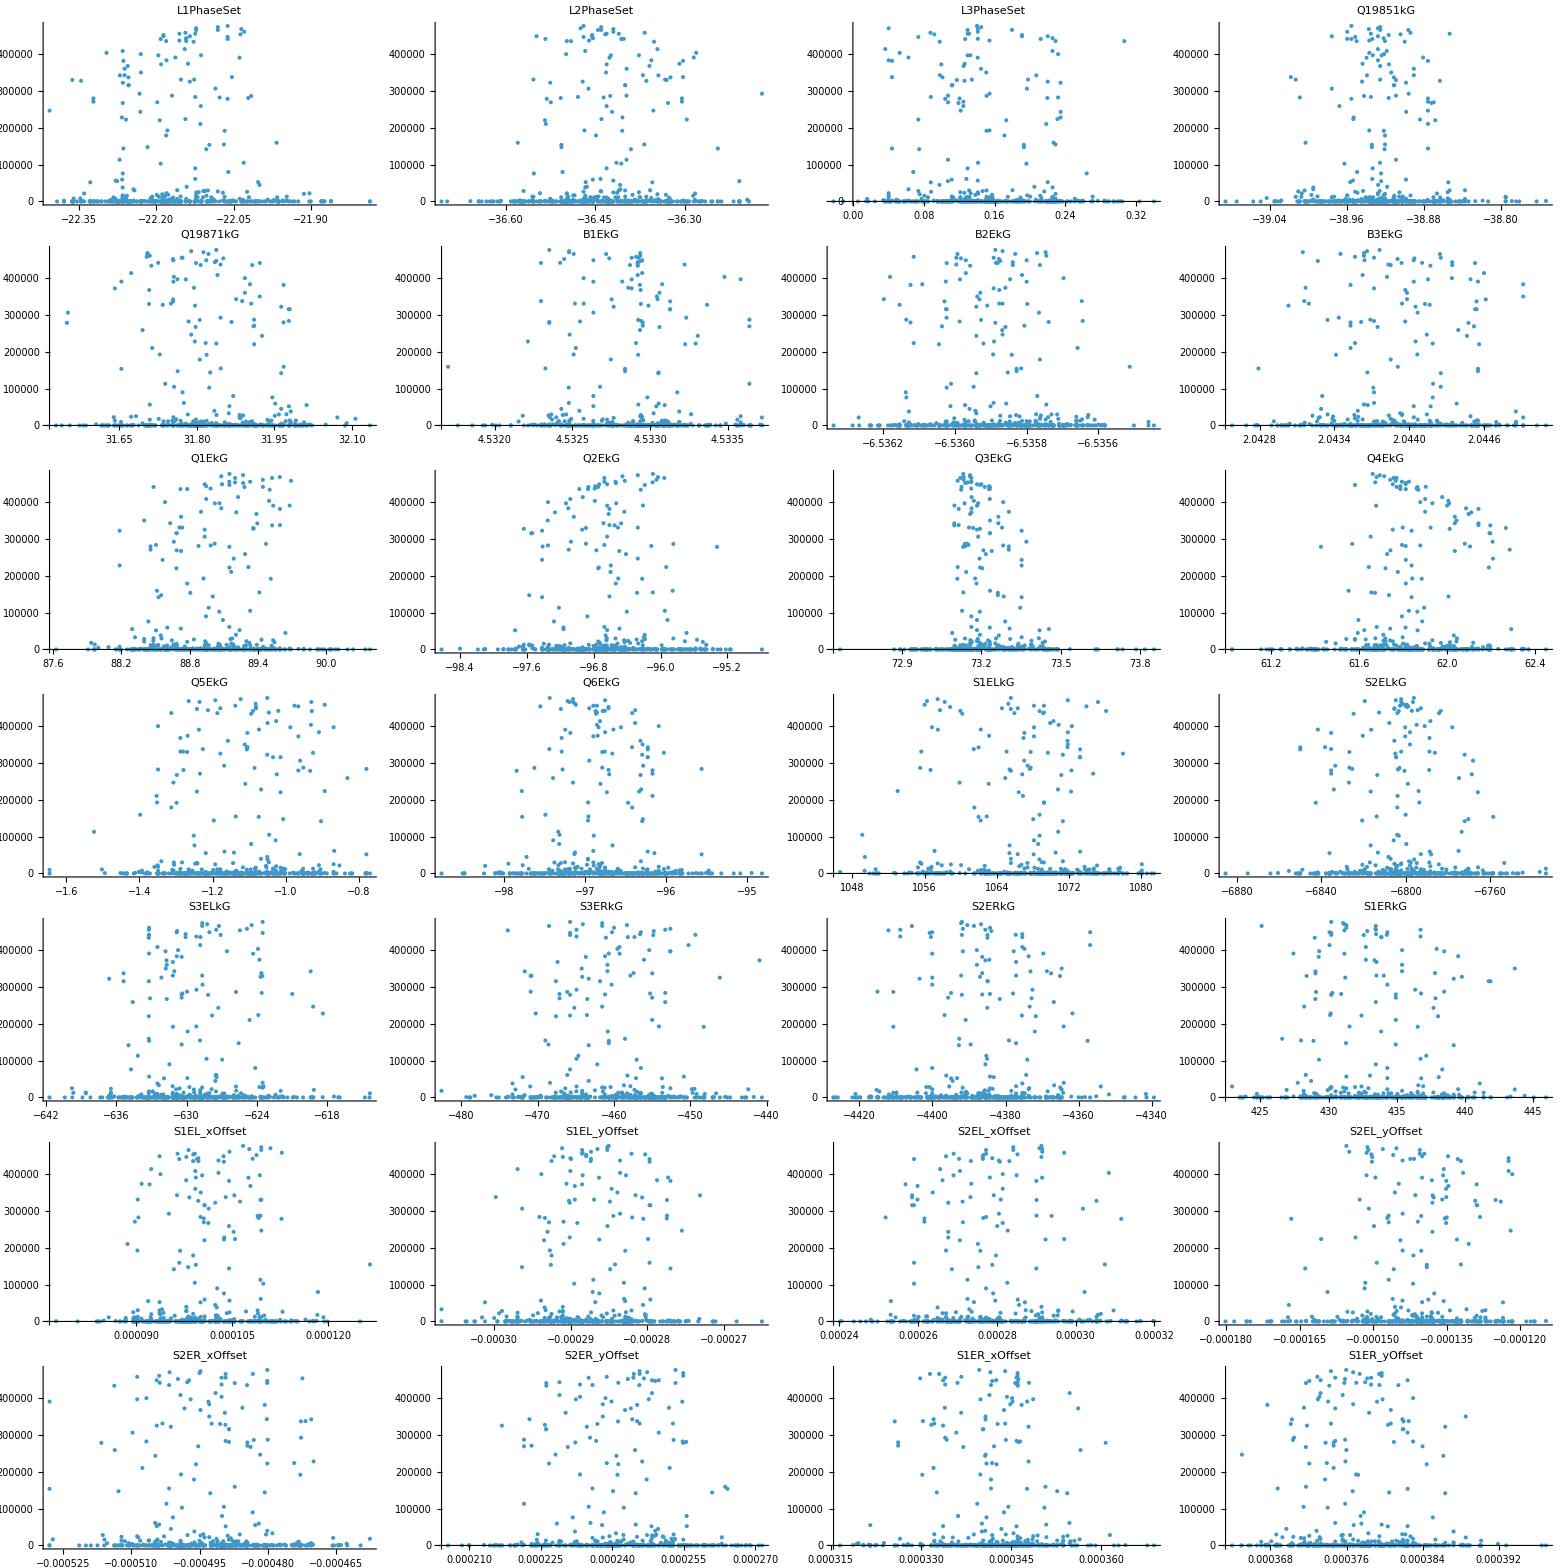

```mathematica
imgArr=ParallelTable[
ListPlot[
{#[key],#["maximizeMe"]}&/@raw,
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All
],
{key,indepVarKeys}
];

displayCols = 4;
Grid[
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
],
Frame->All
]
```

## Plot all

```mathematica
(*This block can get really slow for large numbers of simulations; pare down number of points to plot*)
shotCount = Length[raw[[All,1]]];
indicesToPlot = DeleteDuplicates[Round[Range[1,shotCount,shotCount/1000]]];
```

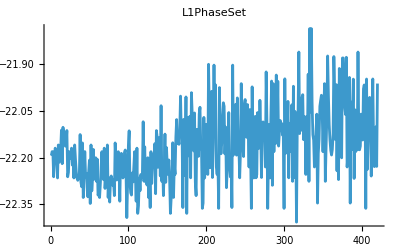
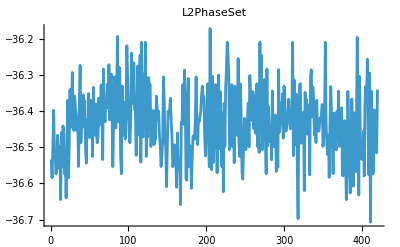
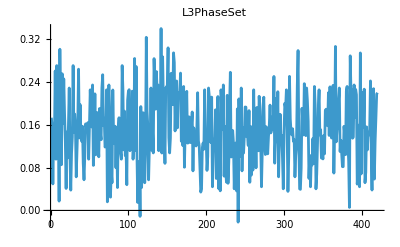
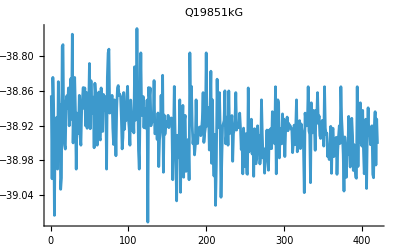
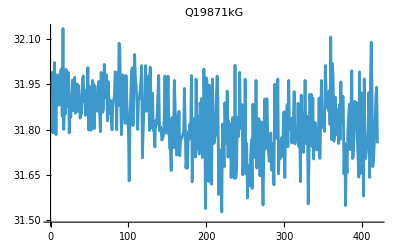
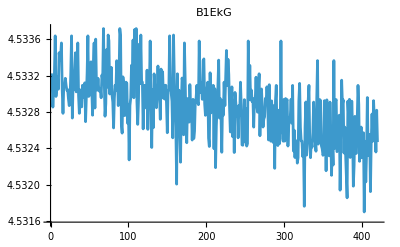
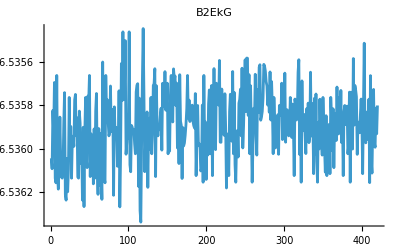
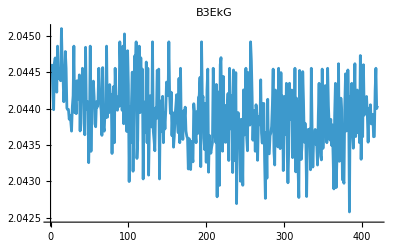
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 0 | 0

```mathematica
imgArr=ParallelTable[
ListPlot[
raw[[indicesToPlot,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Estimate maximizeMe asymptote

There’s no reason at all to think this is valid

```mathematica
(*runningBest = #["maximizeMe"]&/@raw;*)
```

Calculate

Estimated limits: {390833.,441142.,446158.,451173.,501482.}

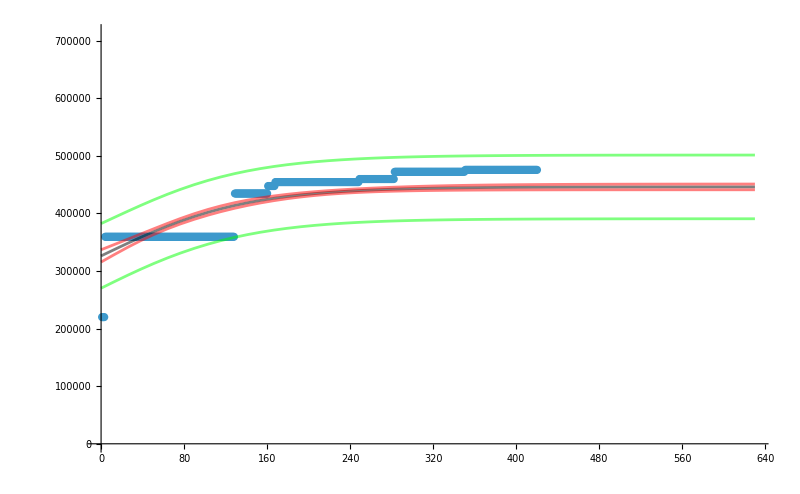

```mathematica
Button["Calculate",

expr = a * Tanh[b ii]+c;
nlm=NonlinearModelFit[
Transpose[{Range[Length[runningBest]],runningBest}],
expr,
{
{a,Max[runningBest]},
{b,1/Length[runningBest]},
{c,Min[runningBest]}
},
ii,
Method->"NMinimize"
];

meanPredictionBands = nlm["MeanPredictionBands"];
singlePredictionBands = nlm["SinglePredictionBands"];
plotMe ={nlm["BestFit"]}~Join~meanPredictionBands~Join~singlePredictionBands;

img = Show[
ListPlot[
Transpose[{Range[Length[runningBest]],runningBest}],
PlotRange->{{0,Length[runningBest]*1.5},{0, Max[runningBest]*1.5}},
ImageSize->800
],

Plot[
plotMe,
{ii,0,Length[runningBest]*1.5},
PlotStyle->{{Opacity[0.5],Black},{Opacity[0.5],Red},{Opacity[0.5],Red},{Opacity[0.5],Green},{Opacity[0.5],Green}},
PlotRange->All
]

];

Print[
"Estimated limits: ",
Sort[
Limit[#,ii->Infinity]&/@plotMe
]
];
Print[img];
]
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,L3PhaseSet,Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ERkG,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ERkG,S2ER_xOffset,S2ER_yOffset,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -22.0618 | -1.74976
L2PhaseSet | -38.6737 | -36.4694 | 2.20435
L3PhaseSet | -1.46329 | 0.140117 | 1.60341
S1EL_xOffset | 0.000385255 | 0.000106732 | -0.000278523
S1EL_yOffset | -0.000241114 | -0.000285014 | -0.0000439001
S2EL_xOffset | -0.00141787 | 0.000291293 | 0.00170916
S2EL_yOffset | 0.0000111705 | -0.000155485 | -0.000166656
S2ER_xOffset | -0.00223816 | -0.000480129 | 0.00175803
S2ER_yOffset | -0.000675996 | 0.000253296 | 0.000929292
S1ER_xOffset | 0.00100714 | 0.00033968 | -0.000667457
S1ER_yOffset | 0.000398456 | 0.000375963 | -0.000022493
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]